I.1 x-πy+5^(1/3)z=0 is a linear equation
I.2 x^2+y^2+z^2=1 is NOT a linear equation
I.3 x^-1+7y+z=(Sin[π/9])^2 is NOT a linear equation
I.4 x+7y+z=Sin[π/9] is a linear equation
I.5 3Cos[x]-4y+z=√3 is NOT a linear equation
I.6 Cos[3]x-4y+z=√3 is a linear equation

II.7

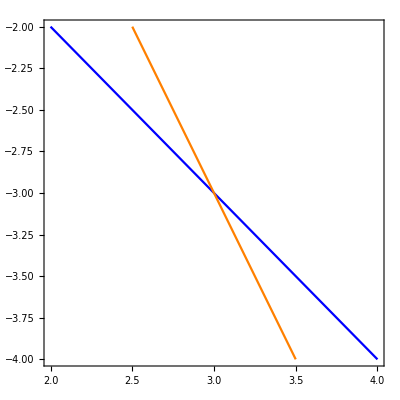

{{x→3,y→-3}}

```mathematica
ContourPlot[{x + y == 0, 2*x + y == 3}, {x, 2, 4}, {y, -4, -2},ContourStyle->{Blue,Orange}]
(*
Piecewise[{{x+y, =0}, {2x+y, =3}}]⇒({{1, 1, 0}, {2, 1, 3}})⇒Subscript[R, 2]-2 Subscript[R, 1]⇒({{1, 1, 0}, {0, -1, 3}})⇒Piecewise[{{x+y, =0}, {-y, =3}}]
y=-3

x+y=0
x=-(-3)
x=3
*)
Solve[{x + y == 0,2*x + y == 3}, {x,y}]
```

II.8

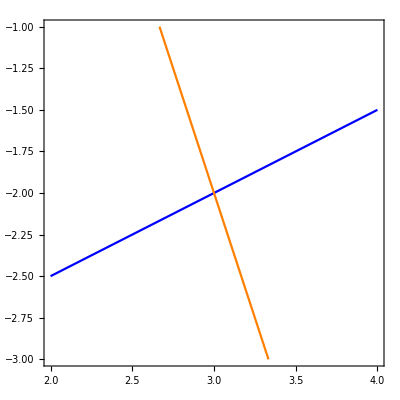

{{x→3,y→-2}}

```mathematica
ContourPlot[{x - 2*y == 7, 3*x + y == 7}, {x, 2, 4}, {y, -3, -1},ContourStyle->{Blue,Orange}]
(*
Piecewise[{{x-2y, =7}, {3x+y, =7}}]⇒({{1, -2, 7}, {3, 1, 7}})⇒Subscript[R, 2]-3 Subscript[R, 1]⇒({{1, -2, 7}, {0, 7, -14}})⇒Piecewise[{{x-2y, =7}, {7y, =-14}}]
y=-2

x-2y=7
x=7+2(-2)
x=3
*)
Solve[{x - 2*y == 7,3*x + y == 7}, {x,y}]
```

II.9

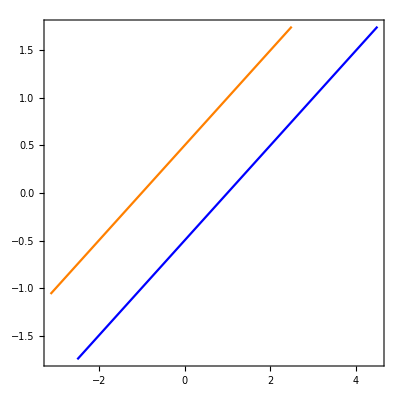

{}

```mathematica
ContourPlot[{3*x - 6*y == 3, -x + 2*y == 1}, {x, -3.125, 4.5}, {y, -1.75, 1.75},ContourStyle->{Blue,Orange}]
(*
Piecewise[{{3x-6y, =3}, {-x+2y, =1}}]⇒({{3, -6, 3}, {-1, 2, 1}})⇒Subscript[R, 2]+1/3 Subscript[R, 1]⇒({{3, -6, 3}, {0, 0, 2}})⇒Piecewise[{{3x-6y, =3}, {0, =2}}]
no solution
*)
Solve[{ 3*x - 6*y == 3,  -x + 2*y == 1}, {x,y}]
```